```mathematica
TableForm[Table[
With[
{g=MinimalSolGraph[max]},
VertexCount[g]->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
SummarizeFormula[form]]],
{max,4,12}]]
```

4→{{4,1}}
5→{{4,1},{5,1}}
6→{{4,1},{5,3},{6,1}}
7→{{4,1},{5,7},{6,6},{7,1}}
8→{{4,1},{5,15},{6,25},{7,10},{8,1}}
9→{{4,1},{5,31},{6,90},{7,65},{8,15},{9,1}}
10→{{4,1},{5,63},{6,301},{7,350},{8,140},{9,21},{10,1}}
11→{{4,1},{5,127},{6,966},{7,1701},{8,1050},{9,266},{10,28},{11,1}}
12→{{4,1},{5,255},{6,3025},{7,7770},{8,6951},{9,2646},{10,462},{11,36},{12,1}}

```mathematica
TableForm[Table[
With[
{g=MinimalSolGraph[max]},
VertexCount[g]->CompleteBaseCoeff[ChromaticPolynomial[g,x]]],
{max,4,12}]]
```

4→{0,0,0,0,1}
5→{0,0,0,0,1,1}
6→{0,0,0,0,1,3,1}
7→{0,0,0,0,1,7,6,1}
8→{0,0,0,0,1,15,25,10,1}
9→{0,0,0,0,1,31,90,65,15,1}
10→{0,0,0,0,1,63,301,350,140,21,1}
11→{0,0,0,0,1,127,966,1701,1050,266,28,1}
12→{0,0,0,0,1,255,3025,7770,6951,2646,462,36,1}

```mathematica
TableForm[Table[
With[
{g=MinimalSolGraph[max]},
VertexCount[g]->NullBaseCoeff[ChromaticPolynomial[g,x]]],
{max,4,12}]]
```

4→{0,-6,11,-6,1}
5→{0,18,-39,29,-9,1}
6→{0,-54,135,-126,56,-12,1}
7→{0,162,-459,513,-294,92,-15,1}
8→{0,-486,1539,-1998,1395,-570,137,-18,1}
9→{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}
10→{0,-4374,16767,-27702,26082,-15498,6048,-1554,254,-24,1}
11→{0,13122,-54675,99873,-105948,72576,-33642,10710,-2316,326,-27,1}
12→{0,-39366,177147,-354294,417717,-323676,173502,-65772,17658,-3294,407,-30,1}

```mathematica
TableForm[Table[
With[
{g=JacobsThalGraph2[max]},
VertexCount[g]->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
SummarizeFormula[form]]],
{max,4,12}]]
```

4→{{4,1}}
5→{{4,1},{5,1}}
6→{{3,1},{4,3},{5,3},{6,1}}
7→{{4,5},{5,10},{6,6},{7,1}}
8→{{3,1},{4,11},{5,30},{6,29},{7,10},{8,1}}
9→{{4,21},{5,91},{6,126},{7,70},{8,15},{9,1}}
10→{{3,1},{4,43},{5,273},{6,525},{7,420},{8,146},{9,21},{10,1}}
11→{{4,85},{5,820},{6,2142},{7,2331},{8,1170},{9,273},{10,28},{11,1}}
12→{{3,1},{4,171},{5,2460},{6,8653},{7,12390},{8,8427},{9,2835},{10,470},{11,36},{12,1}}

```mathematica
TableForm[Table[
With[
{g=JacobsThalGraph2[max]},
VertexCount[g]->CompleteBaseCoeff[ChromaticPolynomial[g,x]]],
{max,4,12}]]
```

4→{0,0,0,0,1}
5→{0,0,0,0,1,1}
6→{0,0,0,1,3,3,1}
7→{0,0,0,0,5,10,6,1}
8→{0,0,0,1,11,30,29,10,1}
9→{0,0,0,0,21,91,126,70,15,1}
10→{0,0,0,1,43,273,525,420,146,21,1}
11→{0,0,0,0,85,820,2142,2331,1170,273,28,1}
12→{0,0,0,1,171,2460,8653,12390,8427,2835,470,36,1}

```mathematica
TableForm[Table[
With[
{g=JacobsThalGraph2[max]},
VertexCount[g]->NullBaseCoeff[ChromaticPolynomial[g,x]]],
{max,4,12}]]
```

4→{0,-6,11,-6,1}
5→{0,18,-39,29,-9,1}
6→{0,-64,154,-137,58,-12,1}
7→{0,210,-565,594,-320,95,-15,1}
8→{0,-664,1992,-2432,1595,-615,141,-18,1}
9→{0,2058,-6839,9533,-7378,3500,-1050,196,-21,1}
10→{0,-6304,23030,-36115,32228,-18158,6734,-1652,260,-24,1}
11→{0,19170,-76425,133172,-134592,87822,-38808,11802,-2448,333,-27,1}
12→{0,-58024,250756,-480554,542325,-402090,206262,-74886,19290,-3465,415,-30,1}

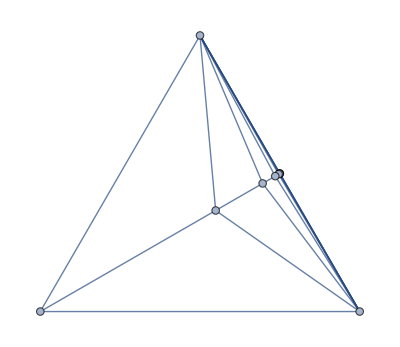

```mathematica
Graph[MinimalSolGraph[10],GraphLayout->"TutteEmbedding"]
```

## And now some calculations

```mathematica
FourFormula[list_]:=Select[list,StringCount[SymbolName[#],"x"]==3&]
```

```mathematica
FiveFormula[list_]:=Select[list,StringCount[SymbolName[#],"x"]==4&]
```

```mathematica
SixFormula[list_]:=Select[list,StringCount[SymbolName[#],"x"]==5&]
```

```mathematica
ToLabels[list_]:=Map[SymbolToLabel[#]&, list]
```

```mathematica
TableForm[Table[
With[
{g=MinimalSolGraph[max]},
With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
With[{four=First[Select[form,StringCount[SymbolName[#],"x"]==3&]]},
With[{good=Select[form,IsRefinement[SymbolToSets[four],SymbolToSets[#]]&]},
{max,ToLabels[ FourFormula[form]],Length[ FiveFormula[good]],Length[ Select[FiveFormula[form],!MemberQ[good,#]&]],Length[ FiveFormula[form]]}
]
]
]
],
{max,4,13}],TableHeadings->{None,{"n","four","good five", "other five", "all five"}}]
```

n | four | good five | other five | all five
4 | 1♁2♁3♁4 | 0 | 0 | 0
5 | 1♁2♁35♁4 | 1 | 0 | 1
6 | 1♁2♁35♁46 | 2 | 1 | 3
7 | 1♁2♁46♁735 | 4 | 3 | 7
8 | 1♁2♁735♁846 | 6 | 9 | 15
9 | 1♁2♁3579♁846 | 10 | 21 | 31
10 | 1♁2♁3579♁468a | 14 | 49 | 63
11 | 1♁2♁468a♁79b35 | 22 | 105 | 127
12 | 1♁2♁79b35♁8ac46 | 30 | 225 | 255
13 | 1♁2♁8ac46♁bd3579 | 46 | 465 | 511

```mathematica
Table[Binomial[2^k-1,2],{k,1,20}]
```

{0,3,21,105,465,1953,8001,32385,130305,522753,2094081,8382465,33542145,134193153,536821761,2147385345,8589737985,34359345153,137438167041,549754241025}

```mathematica
Table[Binomial[2^k-1,2]-2^k,{k,1,20}]
```

{-2,-1,13,89,433,1889,7873,32129,129793,521729,2092033,8378369,33533953,134176769,536788993,2147319809,8589606913,34359083009,137437642753,549753192449}

```mathematica
Table[StirlingS2[Floor[k/2],2]+StirlingS2[Ceiling[k/2],2],{k,1,20}]
```

{0,0,1,2,4,6,10,14,22,30,46,62,94,126,190,254,382,510,766,1022}

```mathematica
Table[(StirlingS2[k,2]),{k,1,20}]
```

{0,1,3,7,15,31,63,127,255,511,1023,2047,4095,8191,16383,32767,65535,131071,262143,524287}

```mathematica
Table[(StirlingS2[Floor[(k+1)/2],2]+StirlingS2[Ceiling[(k+1)/2],2])-(0),{k,1,20}]
```

{0,1,2,4,6,10,14,22,30,46,62,94,126,190,254,382,510,766,1022,1534}

```mathematica
Table[(StirlingS2[k,2])-(StirlingS2[Floor[(k+1)/2],2]+StirlingS2[Ceiling[(k+1)/2],2]),{k,1,50,2}]
```

{0,1,9,49,225,961,3969,16129,65025,261121,1046529,4190209,16769025,67092481,268402689,1073676289,4294836225,17179607041,68718952449,274876858369,1099509530625,4398042316801,17592177655809,70368727400449,281474943156225}

```mathematica
Table[(StirlingS2[k,2])-(StirlingS2[Floor[(k+1)/2],2]+StirlingS2[Ceiling[(k+1)/2],2]),{k,2,50,2}]
```

{0,3,21,105,465,1953,8001,32385,130305,522753,2094081,8382465,33542145,134193153,536821761,2147385345,8589737985,34359345153,137438167041,549754241025,2199020109825,8796086730753,35184359505921,140737463189505,562949903089665}

```mathematica
Table[StirlingS2[2^n-1,2^n-2],{n,1,10}]
```

{0,3,21,105,465,1953,8001,32385,130305,522753}

```mathematica
Table[StirlingS2[n,2],{n,1,10}]
```

{0,1,3,7,15,31,63,127,255,511}

```mathematica
Table[StirlingS2[n,2]^2,{n,1,10}]
```

{0,1,9,49,225,961,3969,16129,65025,261121}

## Solutions as they are spoke

odd and even:

```mathematica
Table[(StirlingS2[k,2])-(StirlingS2[Floor[(k+1)/2],2]+StirlingS2[Ceiling[(k+1)/2],2]),{k,1,50,2}]
```

{0,1,9,49,225,961,3969,16129,65025,261121,1046529,4190209,16769025,67092481,268402689,1073676289,4294836225,17179607041,68718952449,274876858369,1099509530625,4398042316801,17592177655809,70368727400449,281474943156225}

```mathematica
Table[StirlingS2[n,2]^2,{n,1,25}]
```

{0,1,9,49,225,961,3969,16129,65025,261121,1046529,4190209,16769025,67092481,268402689,1073676289,4294836225,17179607041,68718952449,274876858369,1099509530625,4398042316801,17592177655809,70368727400449,281474943156225}

```mathematica
Table[(StirlingS2[k,2])-(StirlingS2[Floor[(k+1)/2],2]+StirlingS2[Ceiling[(k+1)/2],2]),{k,2,50,2}]
```

{0,3,21,105,465,1953,8001,32385,130305,522753,2094081,8382465,33542145,134193153,536821761,2147385345,8589737985,34359345153,137438167041,549754241025,2199020109825,8796086730753,35184359505921,140737463189505,562949903089665}

```mathematica
Table[StirlingS2[2^n-1,2^n-2],{n,1,25}]
```

{0,3,21,105,465,1953,8001,32385,130305,522753,2094081,8382465,33542145,134193153,536821761,2147385345,8589737985,34359345153,137438167041,549754241025,2199020109825,8796086730753,35184359505921,140737463189505,562949903089665}

## Combining new and implied

```mathematica
Table[With[{a=StirlingS2[n,2]^2 ,b=StirlingS2[Floor[(n)],2]+StirlingS2[Ceiling[(n)],2]},
{a,b,a+b, StirlingS2[n*2-1,2]}],{n,1,25}]
```

{{0,0,0,0},{1,2,3,3},{9,6,15,15},{49,14,63,63},{225,30,255,255},{961,62,1023,1023},{3969,126,4095,4095},{16129,254,16383,16383},{65025,510,65535,65535},{261121,1022,262143,262143},{1046529,2046,1048575,1048575},{4190209,4094,4194303,4194303},{16769025,8190,16777215,16777215},{67092481,16382,67108863,67108863},{268402689,32766,268435455,268435455},{1073676289,65534,1073741823,1073741823},{4294836225,131070,4294967295,4294967295},{17179607041,262142,17179869183,17179869183},{68718952449,524286,68719476735,68719476735},{274876858369,1048574,274877906943,274877906943},{1099509530625,2097150,1099511627775,1099511627775},{4398042316801,4194302,4398046511103,4398046511103},{17592177655809,8388606,17592186044415,17592186044415},{70368727400449,16777214,70368744177663,70368744177663},{281474943156225,33554430,281474976710655,281474976710655}}

```mathematica
Table[With[{a=StirlingS2[2^n-1,2^n-2] ,b=StirlingS2[Floor[(n+1)],2]+StirlingS2[Ceiling[(n)],2]},
{a,b,a+b, StirlingS2[n*2,2]}],{n,2,25}]
```

{{3,4,7,7},{21,10,31,31},{105,22,127,127},{465,46,511,511},{1953,94,2047,2047},{8001,190,8191,8191},{32385,382,32767,32767},{130305,766,131071,131071},{522753,1534,524287,524287},{2094081,3070,2097151,2097151},{8382465,6142,8388607,8388607},{33542145,12286,33554431,33554431},{134193153,24574,134217727,134217727},{536821761,49150,536870911,536870911},{2147385345,98302,2147483647,2147483647},{8589737985,196606,8589934591,8589934591},{34359345153,393214,34359738367,34359738367},{137438167041,786430,137438953471,137438953471},{549754241025,1572862,549755813887,549755813887},{2199020109825,3145726,2199023255551,2199023255551},{8796086730753,6291454,8796093022207,8796093022207},{35184359505921,12582910,35184372088831,35184372088831},{140737463189505,25165822,140737488355327,140737488355327},{562949903089665,50331646,562949953421311,562949953421311}}

Now with same n

```mathematica
Style[TraditionalForm[With[{a=StirlingS2[Ceiling[(n)/2],2]^2 ,b=StirlingS2[Ceiling[(n)/2],2]+StirlingS2[Ceiling[(n)/2],2]},
{a,b,a+b, StirlingS2[n,2]}]],40]
```

{(Ceiling[n/2]2)^2,2 Ceiling[n/2]2,(Ceiling[n/2]2)^2+2 Ceiling[n/2]2,n2}

```mathematica
Table[With[{a=StirlingS2[Ceiling[(n)/2],2]^2 ,b=StirlingS2[Ceiling[(n)/2],2]+StirlingS2[Ceiling[(n)/2],2]},
{a,b,a+b, StirlingS2[n,2]}],{n,1,50,2}]
```

{{0,0,0,0},{1,2,3,3},{9,6,15,15},{49,14,63,63},{225,30,255,255},{961,62,1023,1023},{3969,126,4095,4095},{16129,254,16383,16383},{65025,510,65535,65535},{261121,1022,262143,262143},{1046529,2046,1048575,1048575},{4190209,4094,4194303,4194303},{16769025,8190,16777215,16777215},{67092481,16382,67108863,67108863},{268402689,32766,268435455,268435455},{1073676289,65534,1073741823,1073741823},{4294836225,131070,4294967295,4294967295},{17179607041,262142,17179869183,17179869183},{68718952449,524286,68719476735,68719476735},{274876858369,1048574,274877906943,274877906943},{1099509530625,2097150,1099511627775,1099511627775},{4398042316801,4194302,4398046511103,4398046511103},{17592177655809,8388606,17592186044415,17592186044415},{70368727400449,16777214,70368744177663,70368744177663},{281474943156225,33554430,281474976710655,281474976710655}}

```mathematica
Style[FullSimplify[TraditionalForm[With[{a=StirlingS2[2^Floor[(n+1)/2]-1,2^Floor[(n+1)/2]-2] ,b=StirlingS2[Floor[(n+1)/2],2]+StirlingS2[Ceiling[(n+1)/2],2]},
{a,b,a+b, StirlingS2[n,2]}]]],40]
```

{-1+2^Floor[(n+1)/2]-2+2^Floor[(n+1)/2],Ceiling[(n+1)/2]2+Floor[(n+1)/2]2,Ceiling[(n+1)/2]2+-1+2^Floor[(n+1)/2]-2+2^Floor[(n+1)/2]+Floor[(n+1)/2]2,n2}

```mathematica
Table[With[{a=StirlingS2[2^Floor[(n+1)/2]-1,2^Floor[(n+1)/2]-2] ,b=StirlingS2[Floor[(n+1)/2],2]+StirlingS2[Ceiling[(n+1)/2],2]},
{a,b,a+b, StirlingS2[n,2]}],{n,2,50,2}]
```

{{0,1,1,1},{3,4,7,7},{21,10,31,31},{105,22,127,127},{465,46,511,511},{1953,94,2047,2047},{8001,190,8191,8191},{32385,382,32767,32767},{130305,766,131071,131071},{522753,1534,524287,524287},{2094081,3070,2097151,2097151},{8382465,6142,8388607,8388607},{33542145,12286,33554431,33554431},{134193153,24574,134217727,134217727},{536821761,49150,536870911,536870911},{2147385345,98302,2147483647,2147483647},{8589737985,196606,8589934591,8589934591},{34359345153,393214,34359738367,34359738367},{137438167041,786430,137438953471,137438953471},{549754241025,1572862,549755813887,549755813887},{2199020109825,3145726,2199023255551,2199023255551},{8796086730753,6291454,8796093022207,8796093022207},{35184359505921,12582910,35184372088831,35184372088831},{140737463189505,25165822,140737488355327,140737488355327},{562949903089665,50331646,562949953421311,562949953421311}}

## For six elements

```mathematica
Monitor[TableForm[Table[
With[
{g=MinimalSolGraph[max]},
With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
With[{five=Select[form,StringCount[SymbolName[#],"x"]==4&]},
With[{good=Select[form,Fold[Or,Table[IsRefinement[SymbolToSets[fv],SymbolToSets[#]],{fv,five}]]&]},
{max,Length[ FiveFormula[form]],Length[ SixFormula[good]],Length[ Select[SixFormula[form],!MemberQ[good,#]&]],Length[ SixFormula[form]]}
]
]
]
],
{max,4,12}],TableHeadings->{None,{"n","five","good six", "other six", "all six"}}],max]
```

n | five | good six | other six | all six
4 | 0 | 0 | 0 | 0
5 | 1 | 0 | 0 | 0
6 | 3 | 1 | 0 | 1
7 | 7 | 6 | 0 | 6
8 | 15 | 25 | 0 | 25
9 | 31 | 90 | 0 | 90
10 | 63 | 290 | 11 | 301
11 | 127 | 892 | 74 | 966
12 | 255 | 2610 | 415 | 3025

```mathematica
Table[StirlingS2[Floor[k/2],3]+StirlingS2[Ceiling[k/2],3],{k,1,20}]
```

{0,0,0,0,1,2,7,12,31,50,115,180,391,602,1267,1932,3991,6050,12355,18660}